```mathematica
ClearAll["Global`*"]
```

```mathematica
eqnP = λ/k*R*P-(μ + σ*(1-R/k))*P/.{λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M]};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*R*(1-R/k)-((λ/Y)*(R/k)+ρ)*P/.{λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnR},{P,R}]]
```

{{P→0,R→0},{P→0,R→k},{P→(k α Y[M] (λ[M]-μ[M]) (μ[M]+σ[M]))/((λ[M]+σ[M]) (Y[M] ρ[M] σ[M]+λ[M] (μ[M]+Y[M] ρ[M]+σ[M]))),R→(k (μ[M]+σ[M]))/(λ[M]+σ[M])}}

```mathematica
Psol = P/.LVSS[[3]]
Rsol = R/.LVSS[[3]]
```

(k α Y[M] (λ[M]-μ[M]) (μ[M]+σ[M]))/((λ[M]+σ[M]) (Y[M] ρ[M] σ[M]+λ[M] (μ[M]+Y[M] ρ[M]+σ[M])))

(k (μ[M]+σ[M]))/(λ[M]+σ[M])

```mathematica
jac =FullSimplify[{{ D[eqnR,R],D[eqnR,P]},{D[eqnP,R],D[eqnP,P]}}]/.{P->Psol,R->Rsol}
```

{{α-(2 α (μ[M]+σ[M]))/(λ[M]+σ[M])-(α λ[M] (λ[M]-μ[M]) (μ[M]+σ[M]))/((λ[M]+σ[M]) (Y[M] ρ[M] σ[M]+λ[M] (μ[M]+Y[M] ρ[M]+σ[M]))),-ρ[M]-(λ[M] (μ[M]+σ[M]))/(Y[M] (λ[M]+σ[M]))},{(α Y[M] (λ[M]-μ[M]) (μ[M]+σ[M]))/(Y[M] ρ[M] σ[M]+λ[M] (μ[M]+Y[M] ρ[M]+σ[M])),0}}

```mathematica
(* Parameters that go into the model *)
(* Those that rely on mass have been made into functions for better exploration *)

s=1;
B0=4.7*10^(-2);
Em=5774(*J/gram*);
Emprime =7000;
aprime =  B0/Emprime;
η=3/4;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));
Ed=18200; (*J/g*)
k=(*5*)23000;
(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
Y[M_]:=M*Ed/BLam[M]; (*g individual/ g grass*)
(*Predation Mortality*)
p = Exp[palpha + pbeta*Log[M/PM] + pgamma*Log[M/PM]^2];
avgmortratepred[dpred_,palpha_,pbeta_,pgamma_,M_,PM_] :=dpred(( Exp[palpha + pbeta*Log[M/PM] + pgamma*Log[M/PM]^2])/(1+(Exp[palpha + pbeta*Log[M/PM] + pgamma*Log[M/PM]^2])));
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
(*μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   *)

μgen[M_,q0_,α_,texp_]:=((-1+ⅇ^(texp α)) q0)/(texp α)(* this is the consumer death rate*)
dpred =ξ;
(*PM = 10^5;*)
μ[M_] :=μgen[M,a0*M^b0 , a1*M^b1+ avgmortratepred[dpred,1.6332,0.2109,-0.3731,M,PM], a2*M^b2]

B0=4.7*10^(-2);(*W g^−0.75*)
Em=5774;(*J/gram*)
a = B0/Em;
m0[M_]:= (.0558*(1/1000)^.92*M^0.92)*1000;
ϵLam = 0.95;
τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate *)

(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)

E'=7000; (*J/g*)
a'=B0/E';
m[t_,M_]:=M*E^(-a'*t/(M^(1-η)))



(* Two version of Beta-lambda here. The first one doesn't take long to integrate numerically but gives slightly different results from the analytical version below *)
Bλ[M_]=Integrate[B0*m[t,M]^(η),{t,0,τLam[M]}];

BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
Manipulate[
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"},PlotRange->{10^-11,10^5}],
LogLogPlot[(1/M)*Psol/.{ξ->deathdial,PM->10^i},{M,1,1*10^8},Frame->True]
}],
{{deathdial, 1.88*10^-8 },0,4*(1.88*10^-8 )},{{i,5.2},1,6}]
```

```mathematica
10^5.2
```

158489.

```mathematica
Solve[μ[M] == λ[M]/.{ξ->1,PM->1},M]
```

$Aborted

```mathematica
NSolve[Psol==0/.{ξ->1,PM->1},M]
```

$Aborted

The NSM with external mortality

```mathematica
Manipulate[
LogLogPlot[{(μ[M]+ξ),λ[M],σ[M]},{M,1,10^8}],{ξ,10^-10,10^-8}]
```

```mathematica
critxi = ξ/.Solve[λ[M]==ξ*μ[M],ξ]
```

{-(43.9519 M^0.34)/((-1.+ⅇ^(0.5858 M^0.03)) Log[0.0127415/(1.-0.558031/M^0.02)])}

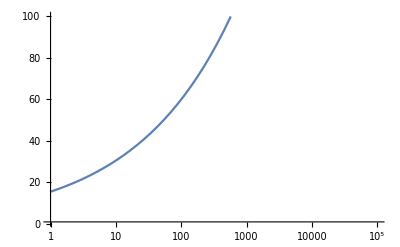

```mathematica
LogLinearPlot[critxi,{M,1,10^5},PlotRange->{1,100}]
```